1.	Разработать программный модуль для формирования системных параметров RSA (модуль, открытый ключ, секретный ключ) на основе заданных номеров простых чисел: Q = Prime[10000-N],          P = Prime[10000+N], где N – номер по списку в группе.

```mathematica
N1=4;
SeedRandom[N1];
Q=Prime[10000-N1];
P=Prime[10000+N1];
rsaParamsModule[Q_,P_]:=Module[{openKey,secretKey, n, phi},
n=P*Q;
phi=(Q-1)*(P-1);
openKey=RandomInteger[{1+1,phi}];
While[GCD[openKey,phi]≠1,openKey=RandomInteger[{1+1,phi}]];
secretKey=PowerMod[openKey,-1,phi];
While[GCD[secretKey,n]≠1,
While[GCD[openKey,phi]≠1,openKey=RandomInteger[{1+1,phi}]];
secretKey=PowerMod[openKey,-1,phi]];
Print["N = ",P*Q];
Print["Open key = ",openKey];
Print["Secret key = ",secretKey];
]
rsaParamsModule[Q,P]
n=10972975879;
openKey=2396097779;
secretKey=4047511979;
```

2.	Импортировать текстовый файл Text-N с номером по списку в группе из папки Plaintext1RSA. Провести анализ кодов текста и привести к виду : 1XXX или 2XXX - четыре десятичных цифры, представляющие собой блок для шифрования в RSA. Например: код пробела 32 представляем как 2000+32=2032.

```mathematica
openText1=" информация должна быть неизвестной.
	Субъект – это активный компонент системы,который может стать причиной потока информации от объекта к субъекту или изменения состояния системы. 
	Объект – пассивный компонент системы, хранящий, принимающий или передающий информацию. Доступ к объекту означает доступ к содержащейся в нем информации.
	Целостность информации обеспечивается в том случае, если данные в системе не отличаются в семантическом отношении от данных в исходных документах, т.е. если не произошло их случайного или преднамеренного искажения или разрушения.
	Целостность компонента или ресурса системы – это свойство компонента или ресурса быть неизменными в семантическом смысле при функционировании системы в условиях случайных  или   преднамеренных   искажений   или   разрушающих   воз-
действий.
	Доступность компонента или ресурса системы – это свойство компонента или ресурса быть доступным для авторизованных законных субъектов системы.
	Под угрозой безопасности АСОИ понимаются возможные воздействия на АСОИ, которые прямо или косвенно могут нанести ущерб ее безопасности.  Ущерб безопасности подразумевает нарушение состояния защищенности информации, содержащейся и обрабатывающейся в АСОИ. С понятием угрозы безопасности тесно связано понятие уязв";
openTextCode1=ToCharacterCode[openText1];
Do[If[openTextCode1[[i]]<1000,openTextCode1[[i]]+=2000],{i,1,Length[openTextCode1]}]
Tally[openTextCode1][[All,1]];
N[Entropy[2,openTextCode1]]
```

(энтропия текста)
3. Построить гистограмму распределения кодов символов открытого текста.

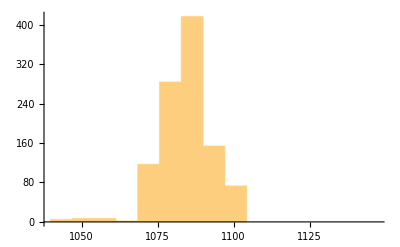

```mathematica
Histogram[openTextCode1]
```

4.	Зашифровать текст на открытом ключе и определить энтропию шифртекста.

```mathematica
cipherCodeText1={};
Do[
AppendTo[
cipherCodeText1,
PowerMod[openTextCode1[[i]],openKey,n]],{i,1,Length[openTextCode1]}]
cipherCodeText1;
N[Entropy[2,cipherCodeText1]]
```

(энтропии открытого текста и шифртекста равны 4.64524)
 5.	Провести расшифрование на секретном ключе.

```mathematica
openTextCode1=Table[0,{i,Length[cipherCodeText1]}];
Do[openTextCode1[[i]]=PowerMod[cipherCodeText1[[i]],secretKey,n],{i,1,Length[cipherCodeText1]}];
Do[If[openTextCode1[[i]]≥2000 && openTextCode1[[i]]<3000,openTextCode1[[i]]-=2000],{i,1,Length[openTextCode1]}];
FromCharacterCode[openTextCode1]
```

(полученный при расшифровке текст совпал с исходным)
 6.	Сформировать из модифицированных блоков открытого текста (см. п.2) десятичные эквиваленты биграмм: {1079,2032}->{10792032}.

```mathematica
openText1=" информация должна быть неизвестной.
	Субъект – это активный компонент системы,который может стать причиной потока информации от объекта к субъекту или изменения состояния системы. 
	Объект – пассивный компонент системы, хранящий, принимающий или передающий информацию. Доступ к объекту означает доступ к содержащейся в нем информации.
	Целостность информации обеспечивается в том случае, если данные в системе не отличаются в семантическом отношении от данных в исходных документах, т.е. если не произошло их случайного или преднамеренного искажения или разрушения.
	Целостность компонента или ресурса системы – это свойство компонента или ресурса быть неизменными в семантическом смысле при функционировании системы в условиях случайных  или   преднамеренных   искажений   или   разрушающих   воз-
действий.
	Доступность компонента или ресурса системы – это свойство компонента или ресурса быть доступным для авторизованных законных субъектов системы.
	Под угрозой безопасности АСОИ понимаются возможные воздействия на АСОИ, которые прямо или косвенно могут нанести ущерб ее безопасности.  Ущерб безопасности подразумевает нарушение состояния защищенности информации, содержащейся и обрабатывающейся в АСОИ. С понятием угрозы безопасности тесно связано понятие уязв";
openTextCode1=ToCharacterCode[openText1];
Do[If[openTextCode1[[i]]<1000,openTextCode1[[i]]+=2000],{i,1,Length[openTextCode1]}]
openCodeText1={};
openCodeText2={};
Do[
AppendTo[openCodeText1,openTextCode1[[2*i-1]]];
AppendTo[openCodeText2,openTextCode1[[2*i]]],
{i,1,IntegerPart[Length[openTextCode1]/2]}]
binaryCodeText1=openCodeText1*10000+openCodeText2
```

7.	Провести шифрование блоков биграмм на открытом ключе. Определить энтропию шифр текста.

```mathematica
cipherCodeBinaryText1={};
Do[AppendTo[cipherCodeBinaryText1, PowerMod[binaryCodeText1[[i]],openKey,n]],{i,1,Length[binaryCodeText1]}]
cipherCodeBinaryText1;
N[Entropy[2,cipherCodeBinaryText1]]
```

8.	Расшифровать полученный шифртекст и вывести  его в виде строки.

```mathematica
binaryCodeText1={};
Do[
AppendTo[binaryCodeText1,PowerMod[cipherCodeBinaryText1[[i]],secretKey,n]],{i,1,Length[cipherCodeBinaryText1]}]
openCodeText1=IntegerPart[binaryCodeText1/10000];
openCodeText2=Mod[binaryCodeText1,10000];
openTextCode1={};
Do[
AppendTo[openTextCode1,openCodeText1[[i]]];
AppendTo[openTextCode1,openCodeText2[[i]]],
{i,1,Length[binaryCodeText1]}]
Do[If[openTextCode1[[i]]≥2000 && openTextCode1[[i]]<3000,openTextCode1[[i]]-=2000],{i,1,Length[openTextCode1]}];
FromCharacterCode[openTextCode1]
```

текст снова совпал с исходным
 9.	Ввести  следующие изменения в Text-N и создать модифицированные строки:
text1– убрать точку в Text-N;
text2 – добавить пробел в Text-N;
text3 – поменять местами две расположенные рядом (разные) буквы в Text-N.

```mathematica
text1=" информация должна быть неизвестной.
	Субъект – это активный компонент системы,который может стать причиной потока информации от объекта к субъекту или изменения состояния системы. 
	Объект – пассивный компонент системы, хранящий, принимающий или передающий информацию. Доступ к объекту означает доступ к содержащейся в нем информации.
	Целостность информации обеспечивается в том случае, если данные в системе не отличаются в семантическом отношении от данных в исходных документах, т.е. если не произошло их случайного или преднамеренного искажения или разрушения.
	Целостность компонента или ресурса системы – это свойство компонента или ресурса быть неизменными в семантическом смысле при функционировании системы в условиях случайных  или   преднамеренных   искажений   или   разрушающих   воз-
действий.
	Доступность компонента или ресурса системы – это свойство компонента или ресурса быть доступным для авторизованных законных субъектов системы.
	Под угрозой безопасности АСОИ понимаются возможные воздействия на АСОИ, которые прямо или косвенно могут нанести ущерб ее безопасности.  Ущерб безопасности подразумевает нарушение состояния защищенности информации, содержащейся и обрабатывающейся в АСОИ С понятием угрозы безопасности тесно связано понятие уязв";
text2=" информация должна быть неизвестной.
	Субъект – это активный компонент системы,который может стать причиной потока информации от объекта к субъекту или изменения состояния системы. 
	Объект – пассивный компонент системы, хранящий, принимающий или передающий информацию. Доступ к объекту означает доступ к содержащейся в нем информации.
	Целостность информации обеспечивается в том случае, если данные в системе не отличаются в семантическом отношении от данных в исходных документах, т.е. если не произошло их случайного или преднамеренного искажения или разрушения.
	Целостность компонента или ресурса системы – это свойство компонента или ресурса быть неизменными в семантическом смысле при функционировании системы в условиях случайных  или   преднамеренных   искажений   или   разрушающих   воз-
действий.
	Доступность компонента или ресурса системы – это свойство компонента или ресурса быть доступным для авторизованных законных субъектов системы.
	Под угрозой безопасности АСОИ понимаются возможные воздействия на АСОИ, которые прямо или косвенно могут нанести ущерб ее безопасности.  Ущерб безопасности подразумевает нарушение состояния защищенности информации, содержащейся и обрабатывающейся в АСОИ. С понятием угрозы безопасности тесно связано понятие уязв ";
text3=" ниформация должна быть неизвестной.
	Субъект – это активный компонент системы,который может стать причиной потока информации от объекта к субъекту или изменения состояния системы. 
	Объект – пассивный компонент системы, хранящий, принимающий или передающий информацию. Доступ к объекту означает доступ к содержащейся в нем информации.
	Целостность информации обеспечивается в том случае, если данные в системе не отличаются в семантическом отношении от данных в исходных документах, т.е. если не произошло их случайного или преднамеренного искажения или разрушения.
	Целостность компонента или ресурса системы – это свойство компонента или ресурса быть неизменными в семантическом смысле при функционировании системы в условиях случайных  или   преднамеренных   искажений   или   разрушающих   воз-
действий.
	Доступность компонента или ресурса системы – это свойство компонента или ресурса быть доступным для авторизованных законных субъектов системы.
	Под угрозой безопасности АСОИ понимаются возможные воздействия на АСОИ, которые прямо или косвенно могут нанести ущерб ее безопасности.  Ущерб безопасности подразумевает нарушение состояния защищенности информации, содержащейся и обрабатывающейся в АСОИ. С понятием угрозы безопасности тесно связано понятие уязв";
```

10. Найти расстояние Дамерау-Левенштейна (DLD) - минимальное количество операций вставки одного символа, удаления одного символа и замены одного символа на другой, необходимых для превращения одной строки в другую- (DamerauLevenshteinDistance[,]) между строкой Text-N и строками text1, text2, text3.

```mathematica
DamerauLevenshteinDistance[openText1,text1]
DamerauLevenshteinDistance[openText1,text2]
DamerauLevenshteinDistance[openText1,text3]
```

11. Найти расстояние Дамерау-Левенштейна (DamerauLevenshteinDistance[,]) между значениями хэш-функций Hash[] строки Text-N и значениями хэш-функций строк text1, text2, text3.

```mathematica
hashMsg=Hash[openText1]
hash1=Hash[text1]
hash2=Hash[text2]
hash3=Hash[text3]
```

```mathematica
DamerauLevenshteinDistance[ToString[hashMsg],ToString[hash1]]
DamerauLevenshteinDistance[ToString[hashMsg],ToString[hash2]]
DamerauLevenshteinDistance[ToString[hashMsg],ToString[hash3]]
```

12. Определить расстояние ДЛ между  значениями  хэш-функций строк Text-N и text1 для алгоритмов хэширования, приведенных в таблице.

```mathematica
DamerauLevenshteinDistance[openText1,text1]
DamerauLevenshteinDistance[ToString[Hash[openText1,"CRC32"]],ToString[Hash[text1,"CRC32"]]]
DamerauLevenshteinDistance[ToString[Hash[openText1,"MD5"]],ToString[Hash[text1,"MD5"]]]
DamerauLevenshteinDistance[ToString[Hash[openText1,"SHA"]],ToString[Hash[text1,"SHA"]]]
DamerauLevenshteinDistance[ToString[Hash[openText1,"SHA256"]],ToString[Hash[text1,"SHA256"]]]
DamerauLevenshteinDistance[ToString[Hash[openText1,"SHA384"]],ToString[Hash[text1,"SHA384"]]]
DamerauLevenshteinDistance[ToString[Hash[openText1,"SHA512"]],ToString[Hash[text1,"SHA512"]]]
```

13. Преобразовать свою фамилию и имя в числовой код  m (а->1, ..я->32), получить криптограмму с зашифровав m на секретном ключе ks. Рассмотреть два варианта: разбиение m на максимальное число элементов и разбиение (или его отсутствие) m на минимально возможное число элементов, при этом допускается изменение параметров RSA.

```mathematica
openText1="балашовсавва";
charText1=Characters[openText1];
msgCodeMinList={};
Do[
AppendTo[msgCodeMinList,ToCharacterCode[charText1[[i]]]-1071],
{i,1,StringLength[openText1]}]
msgCodeMinList=Flatten[msgCodeMinList];
msgCodeMax=FromDigits[Flatten[Table[PadLeft[IntegerDigits[msgCodeMinList[[i]]],2],{i,1,Length[msgCodeMinList]}]]];
SeedRandom[N1];
RandomPrime[{Sqrt[100^11],Sqrt[100^11]*10},2];
rsaParamsModule[892665323731,350261647993]
nLong=312666427396224911421883;
openKeyLong=95459891171862768459367;
secretKeyLong=52592236725673796713063;
cryptCodeMinList={};
Do[
AppendTo[
cryptCodeMinList,
PowerMod[msgCodeMinList[[i]],secretKeyLong, nLong]],
{i,1,Length[msgCodeMinList]}]
cryptCodeMinList
cryptCodeMax=PowerMod[msgCodeMax, secretKeyLong,nLong]
```

14. Расшифровать два варианта криптограммы с на ключе ko и получить m.

```mathematica
msgCodeMinList={};
Do[
AppendTo[
msgCodeMinList,
PowerMod[cryptCodeMinList[[i]],openKeyLong, nLong]],
{i,1,Length[cryptCodeMinList]}]
msgCodeMinList;
FromCharacterCode[msgCodeMinList+1071]
```

15. Преобразовать строку хеш-кода сообщения m в последовательность (список) чисел при минимальном возможном числе элементов шифрования, определить длину этого списка и подготовить два новых списка для шифр текста и восстановленного (расшифрованного) хеш-кода. Номер варианта хэш-функции Nmod5+1:
-Graphics-

```mathematica
Mod[4,5]+1
msgHash=Hash[openText1,"SHA512"];
msgHashList=IntegerDigits[msgHash];
Length[msgHashList]
msgHashList=PadLeft[msgHashList,120];
msgHashList=Partition[msgHashList,20];
Do[
msgHashList[[i]]=FromDigits[msgHashList[[i]]],
{i,1,Length[msgHashList]}]
msgHashList
Length[msgHashList]
cryptHashList=Table[0,{i,6}];
hashFromCryptList=Table[0,{i,6}];
```

16. Провести операцию шифрования хеш-кода на ключе ks и зафиксировать результат.

```mathematica
Do[
cryptHashList[[i]]=PowerMod[msgHashList[[i]],secretKeyLong,nLong],
{i,1,Length[msgHashList]}]
cryptHashList
```

17. Провести операцию расшифрования хеш-кода на ключе ko и зафиксировать результат.

```mathematica
Do[
hashFromCryptList[[i]]=PowerMod[cryptHashList[[i]],openKeyLong,nLong],
{i,1,Length[cryptHashList]}]
hashFromCryptList
```

18. Сравнить результат, полученный в п. 17 с исходным хэш-кодом п.15.

```mathematica
msgHashList;
hashFromCryptList;
HammingDistance[msgHashList,hashFromCryptList]
Do[
If[msgHashList[[i]]== hashFromCryptList[[i]],
Print["совпадают"],
Print["не совпадают"];Break[]],
{i,1,Length[msgHashList]}]
```